```mathematica
Get[ResourceFunction["NotebookRelativePath"][{"Packages", "Utils.wl"}]]
```

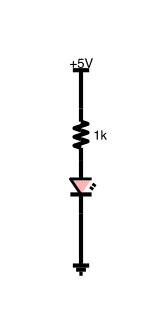
```mathematica
dave=-Graphics-;
```

```mathematica
InputForm[dave];
```

```mathematica
Manipulate[carl[c,v "V"],{c,ColorSlider}, {v, 0, 5, 0.5},SaveDefinitions->True]
```

Show what’s happening to the current

Plot voltage over current

BURN the LED

Show parameters for the LED

## What’s happening to current

```mathematica
ledColor[voltage_, maxVoltage_] := RGBColor[0, reMap[voltage, 0, maxVoltage, 0, 1], 0]
```

```mathematica
ledManipulate =Manipulate[
Row[
{carl[ledColor[v, 5],v "V"],VerticalGauge[current[v, 220], {0, 0.1}]}],{v, 0, 5, 0.5},SaveDefinitions->True
]
```

```mathematica
Export["test4.gif",ledManipulate]
```

test4.gif